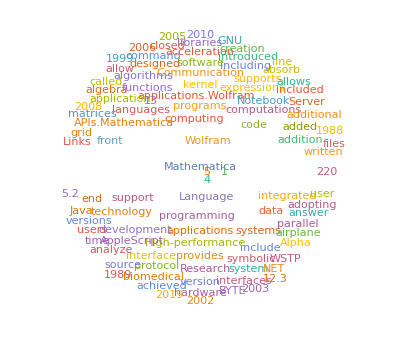

```mathematica
WordCloud[WikipediaData["Mathematica"]]
```

```mathematica
Crash Course in Mathematica for Graduate Students
```

Course Crash for Graduate in Mathematica Students

## Introduction Lesson 1

In MATHEMATICA we can solve symbolic expressions

```mathematica
Solve[a x^2+b x+c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

and solve maths problem like ODEs

```mathematica
DSolve[{x''[t]+3 x'[t]+2x[t]==0, 
x[0]==1, x'[0]==0}, x[t], t ]
```

{{x[t]→ⅇ^(-2 t) (-1+2 ⅇ^t)}}

It is possible to assign a particular value to a variable

```mathematica
a = 2; (*and suppress undesired outputs*)
b = 3;
a + b
```

5

It is possible to compute integrals

```mathematica
Integrate[Sin[x]/x, {x, -Infinity, Infinity}]
```

π

also in a eye-candy way [2]

```mathematica
∫_(-∞)^(+∞) Sin[x]/x ⅆx
```

π

It is easy to make simple plots

```mathematica
func = A Sin[ω t + ϕ];
parameters = {A-> 2, ω->0.3, ϕ-> 0.1};
ReplaceAll[func, parameters] (*a lot of handy shortcuts exist!*)
```

2 Sin[0.1+0.3 t]

```mathematica
func /. parameters
```

2 Sin[0.1+0.3 t]

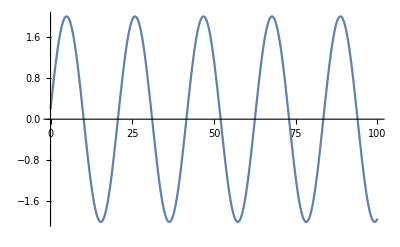

```mathematica
Plot[%, {t, 0, 100}]
```

Obviously you must specifies numerical values for all the parameters, or you can manipulate them...

```mathematica
Manipulate[Plot[A Sin[ω t + ϕ], {t, 0, 100}],{ A, 2, 10}, {ω, 0.3, 1}, {ϕ, 0.1, 10}]
```

You can also manipulate different objects

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}]
```

The idea now is to solve some simple (if you have a bachelor degree in physics) physical problems using MATHEMATICA. Doing this we will discover the main feature of this language.
All the exercise in this lessons are taken from [1]. A more exhaustive treatment can be found in this book. A suggested reading.

## Moving object with non-trivial EoM

Consider an object with the following EoM

Find velocity and acceleration. Plots these along with the position on a single graph with legends. Find the time(s) at which there is no net force on the object.

```mathematica
position[t_]=5t Exp[-t^2]
velocity[t_]= D[position[t], t]
acceleration[t_]=D[velocity[t], t]
```

5 ⅇ^(-t^2) t

5 ⅇ^(-t^2)-10 ⅇ^(-t^2) t^2

-30 ⅇ^(-t^2) t+20 ⅇ^(-t^2) t^3

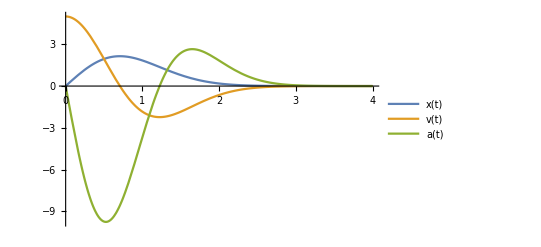

```mathematica
Plot[{position[t], velocity[t], acceleration[t]}, {t, 0,4 }, PlotLegends->{"x(t)", "v(t)", "a(t)"}, PlotRange->Full]
```

```mathematica
Solve[acceleration[t]==0, t, Assumptions->{t≥0}]
```

{{t→0},{t→√(3/2)}}

```mathematica
Limit[acceleration[t], t->∞]
```

0

## Gravity near the Earth’s surface

Find an expression up to second order for the modification to g for an object at the height h. We need to find a small parameter to expand in series on it.

```mathematica
force = G m M / (R+h)^2;
Series[force/.h-> x R, {x, 0, 2}];
forcex = Normal[%]/.x-> h/R
```

(3 G h^2 m M)/R^4-(2 G h m M)/R^3+(G m M)/R^2

Now we can express G in term of the usual gravity acceleration g.

```mathematica
grepl = Solve[g==G M / R^2, G];
forcex/.grepl
```

{g m+(3 g h^2 m)/R^2-(2 g h m)/R}

## Pendulum period

Consider a very standard pendulum: string of length l with a blob of mass m in the end. We know the period is 2π √(l/g) but this is accurate only if the maximum displacement satisfies θ_0<<1 . How to find an expression for the period as a function of θ_0?

From energy conservation we have that energy at θ = θ_0 is equal to the energy at θ = 0.  Thus

We can reduce this equation to an expression for the angular velocity .

θ/t==-√2 √(g/l) √(cos θ-cos θ_0)

(We choose the minus sign because we’ll be thinking about the quarter period of the pendulum if it is released from rest at , hence the angle is decreasing.
The period is four times the time it takes to go from  to .

This is a scary integral and there is no closed analytic form for it, but it is no problem for MATHEMATICA.

```mathematica
int = Integrate[1/(√(Cos[θ]- Cos[θ0])), {θ, θ0, 0}, Assumptions->{θ0>0 && θ0< Pi}]
```

-(2 EllipticF[θ0/2,Csc[θ0/2]^2])/(√(1-Cos[θ0]))

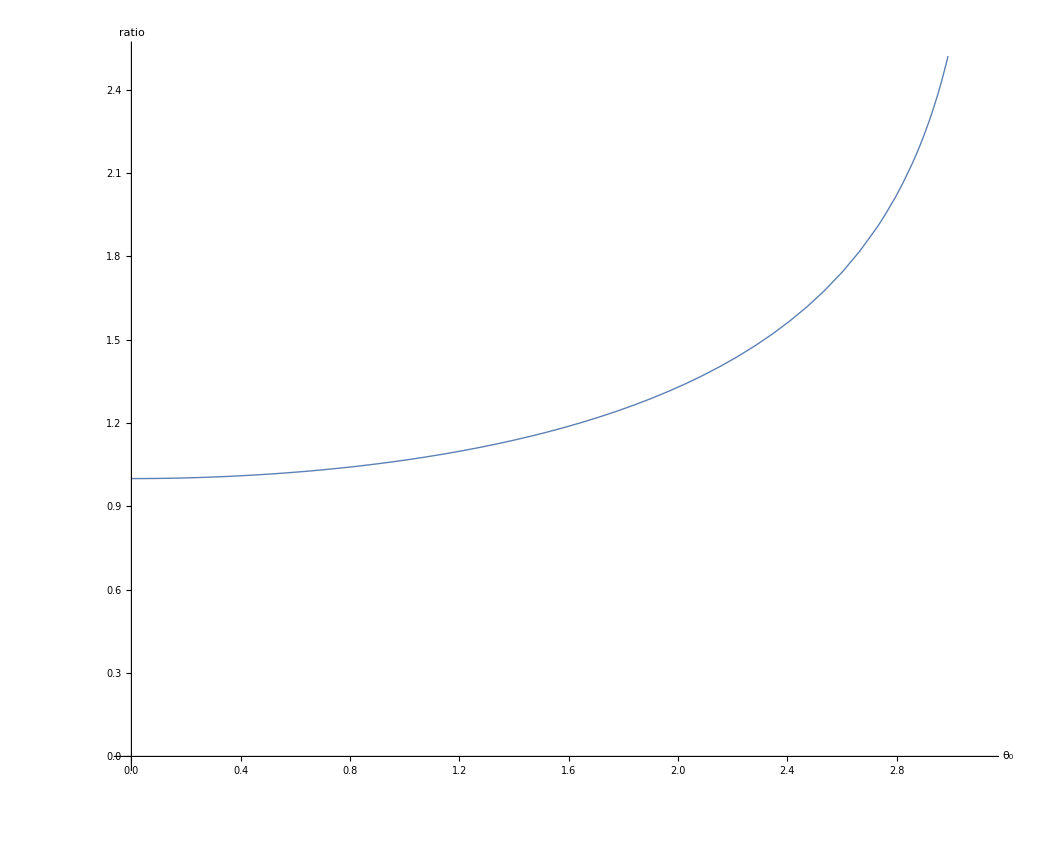

```mathematica
period = -4 √(l/(2g))int;
ratio = period / (2π √(l/g));
Plot[ratio, {θ0, 0, 0.99Pi},PlotStyle->Thick, AspectRatio->Full, AxesLabel->{Subscript[θ, 0], "ratio"}, AxesOrigin->{0, 0}]
```

## A Falling Ball with Drag

Consider a mass , initially at rest, dropped from a height  and subject to a linear drag force  proportional to the velocity.
Find an expression for its height as a function of time and plot it for various value of .

We need to solve the following differential equation

```mathematica
Clear[m, g]
Clear[b]
```

```mathematica
DSolve[{m y''[t]==-m g-b y'[t], y[0]==h, y'[0]==0} , y, t];
height=Simplify@First[y[t]/.%]
```

h+(g m (m-ⅇ^(-(b t)/m) m-b t))/b^2

Check the limit

```mathematica
Limit[height, b->0]
```

h-(g t^2)/2

```mathematica
mgh={m->0.1, g->9.8, h->100};
m1=Manipulate[
Plot[height/.mgh/.b->drag, {t, 0, 15},
PlotRange->{0, 100}, 
AxesLabel->{"t", "h(t)"}],
{drag, 0.0001, 1}]
```

Instead the velocity is

```mathematica
velocity=D[height, t]
```

((-b+b ⅇ^(-(b t)/m)) g m)/b^2

```mathematica
Limit[velocity, t->∞]
```

ConditionalExpression[-(g m)/b, g∈ℝ&&b m>0]

```mathematica
Plot[Evaluate@Table[velocity/.mgh, {b, {0.001,0.005, 0.01,0.05, 0.1 }}], {t, 0, 100},PlotLabels->{0.001,0.005, 0.01,0.05, 0.1 }] (*here I used labels instead of legends*)
```

-Graphics-

## Fourier Series

Consider the function . Obtain and plot the Fourier series of this function. 
Since it is an odd function only the sine components should be different from zero.

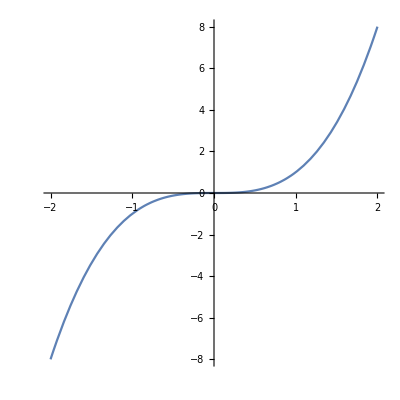

```mathematica
f[x_]=x^3;
Plot[f[x], {x, -2, 2}, AspectRatio->1]
```

```mathematica
a[n_]=1/Pi Integrate[f[x]*Cos[n*x], {x, -Pi, Pi}]
b[n_]=1/Pi Integrate[f[x]*Sin[n*x], {x, -Pi, Pi}]
```

Set::write: Tag Integer in 2[n_] is Protected.

0

(-2 n π (-6+n^2 π^2) Cos[n π]+6 (-2+n^2 π^2) Sin[n π])/(n^4 π)

```mathematica
Table[b[n], {n ,1, 10}] (*the first 10 coefficients*)
```

{2 (-6+π^2),1/4 (6-4 π^2),2/27 (-6+9 π^2),1/32 (6-16 π^2),2/125 (-6+25 π^2),1/108 (6-36 π^2),2/343 (-6+49 π^2),1/256 (6-64 π^2),2/729 (-6+81 π^2),1/500 (6-100 π^2)}

It is easy to obtain the series now and do a comparison

```mathematica
F[x_, Nmax_]:=Sum[b[n]*Sin[n x], {n, 1, Nmax}]  (*:= instead of = maintain the rhs in a unevaluated form*)
Manipulate[Plot[{f[x], F[x, Nmax]}, {x, -Pi, Pi}], {Nmax, 2, 20}]
```

## References

[1] A Mathematica Primer for Physicists, Jim Napolitano
[2] https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
[3] https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
[4] https://reference.wolfram.com/language/tutorial/Lists.html#2534
[5] https://demonstrations.wolfram.com/2DWavePropagation/
[6] https://mathematica.stackexchange.com/questions/134609/why-should-i-avoid-the-for-loop-in-mathematica
[7] https://reference.wolfram.com/language/ref/Module.html

```mathematica
Other Links
```

Links Other

I used these links as a support during the lesson.

- Archives: https://www.wolframphysics.org/archives/index/
- Keyboard Shortcuts: https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
- Demonstration Projects: https://demonstrations.wolfram.com/
- Wolfram Community: https://community.wolfram.com/
- Wolfram Documentation (First function): https://reference.wolfram.com/language/ref/Find.html?q=Find
- Wolfram syntax: https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616